# Updated code

```mathematica
ClearAll["Global`*"];
{brown,green,beige,blue}=RGBColor/@{"#d80125","#6ed855","#f0d933","#165e83"}
(*parameters*)
nu=1. (*heat conductivity*);
SimTime=0.15;
BoxSize=1;
{tMin,tMax}={0,SimTime} (*time*);
{xMin,xMax}={-BoxSize/2.,BoxSize/2.} (*x coordinate*);
xgr=128;dx=BoxSize/(xgr-1);
tgr=6144;dt=SimTime/(tgr-1);
std=0.1; (*sigma of the random variable*)

nu*dt/dx^2<=1/2 (*for nbumerical stability*)
```

{RGBColor[0.8470588235294118, 0.00392156862745098, 0.1450980392156863],RGBColor[0.43137254901960786, 0.8470588235294118, 0.3333333333333333],RGBColor[0.9411764705882353, 0.8509803921568627, 0.2],RGBColor[0.08627450980392157, 0.3686274509803922, 0.5137254901960784]}

True

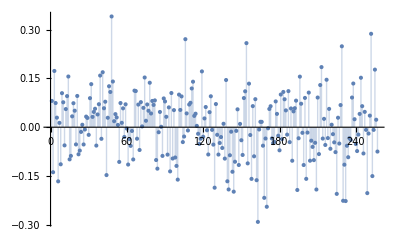

```mathematica
(*Initial conditions NO NEED TO RUN THIS EVERY TIME*)Xi=RandomFunction[WhiteNoiseProcess[std],{1,2*xgr+1}];
ListPlot[Xi,Filling->Axis]
(*To obtain values,run Xi["Values"][[i]],i=1,...,2*xgr+1*)
```

```mathematica
logphiinidata[n_]:=Xi["Values"][[2*xgr+1]]+Sum[Xi["Values"][[i]]*Sin[2*Pi*i*n/(xgr-1)]+Xi["Values"][[i+xgr]]*Cos[2*Pi*i*n/(xgr-1)],{i,1,5}]
data=Array[logphiinidata[#-1]&,xgr];

Export["logphiini.dat",data];
```

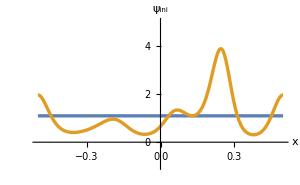

```mathematica
Clear[itpphiini,hom]
dataimp=Import["logphiini.dat"];
dataimpext=Append[dataimp,dataimp[[1]]];
itpimpdata=Interpolation[Table[{j,dataimpext[[j]]},{j,xgr}],InterpolationOrder->3];
itpphiini[x_?NumericQ]:=Exp[-itpimpdata[(x-xMin)/dx+1][[1]]];

hom=Sum[itpphiini[xMin+(i-1)*dx],{i,1,xgr}]/xgr/BoxSize;

thickness=0.04;colorIni=gray;colorFin=sora;
graph1=Plot[{hom,itpphiini[x]},{x,xMin,xMax},AxesLabel->{"x","ψ_ini"},BaseStyle->{FontSize->12,FontFamily->"Latin Modern Roman"},ImageSize->300,PlotRange->{-1,5},PlotStyle->{{Thickness[thickness/5],sakura},{Thickness[thickness/5],aomidori}}]
```

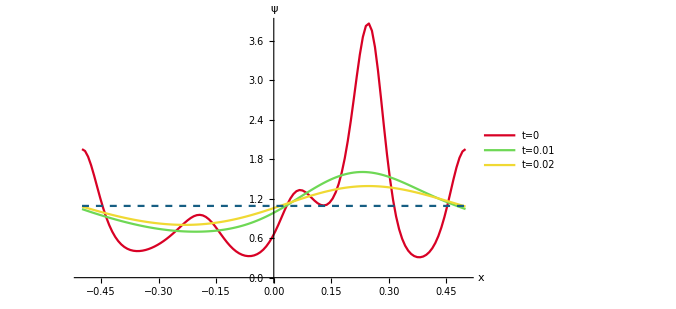

```mathematica
xGrid=Range[xMin,xMax,dx];
phi0={};
For[i=1,i<=xgr,i++,AppendTo[phi0,itpphiini[xGrid[[i]]]]];
phi=phi0;
results={phi};

For[t=1,t<=tgr-1,t++,phiNew=phi;
For[i=2,i<=xgr-1,i++,phiNew[[i]]=phi[[i]]+nu*dt/dx^2*(phi[[i-1]]-2*phi[[i]]+phi[[i+1]]);];
phiNew[[1]]=phi[[1]]+nu*dt/dx^2*(phi[[xgr-1]]-2*phi[[1]]+phi[[2]]) (*PBC*);
phiNew[[xgr]]=phiNew[[1]] (*PBC*);
phi=phiNew;
AppendTo[results,phi];];

graph2=ListLinePlot[{results[[1]],results[[410]],results[[820]]},DataRange->{xMin,xMax},PlotRange->All,PlotStyle->{brown,green,beige},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},ImageSize->500,PlotLegends->Placed[LineLegend[{"t=0","t=0.01","t=0.02"}],{Right,Top}],AxesLabel->{"x","ψ"}];
graph22=Plot[hom,{x,xMin,xMax},AxesLabel->{"x",Subscript["ψ","ini"]},BaseStyle->{FontSize->30,FontFamily->"Latin Modern Roman"},ImageSize->500,PlotRange->{-1,5},PlotStyle->{Dashed,blue}];
(*test*)
graph222=Plot[itpphith[x,0.02],{x,xMin,xMax},PlotStyle->{{Dotted,Red}}];

Show[graph2,graph22]
Export["phi.pdf",%]
```

```mathematica
u0={};
approxu0={};
AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/results[[1]][[1]]];
AppendTo[approxu0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/hom];
For[i=2,i<=xgr-1,i++,AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[i+1]]-results[[1]][[i-1]])/results[[1]][[i]]];
AppendTo[approxu0,-(2.*nu/(2.*dx))*(results[[1]][[i+1]]-results[[1]][[i-1]])/hom];];
AppendTo[u0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/results[[1]][[xgr]]];
AppendTo[approxu0,-(2.*nu/(2.*dx))*(results[[1]][[2]]-results[[1]][[xgr-1]])/hom];
u=u0;
approxu=approxu0;
uresults={u};
approxuresults={approxu};

For[t=1,t<=tgr,t++,uNew=u;
approxuNew=approxu;
uNew[[1]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/results[[t]][[1]];
approxuNew[[1]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/hom;
For[i=2,i<=xgr-1,i++,uNew[[i]]=-(2.*nu/(2.*dx))*(results[[t]][[i+1]]-results[[t]][[i-1]])/results[[t]][[i]];
approxuNew[[i]]=-(2.*nu/(2.*dx))*(results[[t]][[i+1]]-results[[t]][[i-1]])/hom;];
uNew[[xgr]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/results[[t]][[xgr]];
approxuNew[[xgr]]=-(2.*nu/(2.*dx))*(results[[t]][[2]]-results[[t]][[xgr-1]])/hom;
u=uNew;
approxu=approxuNew;
AppendTo[uresults,u];
AppendTo[approxuresults,approxu];];

graph3=ListLinePlot[{uresults[[1]],uresults[[41]],uresults[[1227]]},DataRange->{xMin,xMax},PlotRange->All,ImageSize->500,PlotStyle->{brown,green,beige},PlotLegends->Placed[LineLegend[{"τ=0","τ=0.001","τ=0.005"}],{Right,Top}],AxesLabel->{"x","u"},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"}];
graph4=ListLinePlot[{approxuresults[[1]],approxuresults[[41]],approxuresults[[1227]]},DataRange->{xMin,xMax},PlotRange->All,ImageSize->500,PlotStyle->{{Dashed,brown},{Dashed,green},{Dashed,beige}},AxesLabel->{"x",Subscript["u","approx"]},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"}];
(*test*)
graph44=Plot[uth[x,tMin+1227*dt],{x,xMin,xMax},PlotStyle->{{Dotted,Red}}];
```

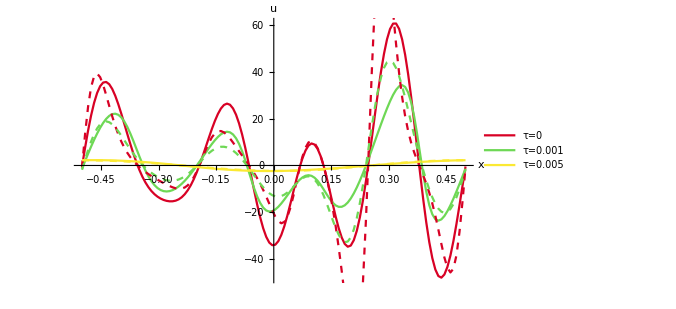

```mathematica
Show[graph3,graph4]
```

```mathematica
Reynolds={};
Reynolds2={};
For[t=1,t<=tgr,t++,urms2=0;
dudxrms2=0;
For[i=1,i<=xgr,i++,urms2=urms2+uresults[[t]][[i]]^2;
If[!(i==1||i==xgr),dudxrms2=dudxrms2+(1/4.)*(uresults[[t]][[i+1]]-uresults[[t]][[i-1]])^2/dx^2]];
urms=Sqrt[urms2/xgr];
dudxrms=Sqrt[dudxrms2/(xgr-2)];
AppendTo[Reynolds,{tMin+t*dt,urms^2/(nu*dudxrms)}];
AppendTo[Reynolds2,{tMin+t*dt,urms^4/(nu*dudxrms)^2}];];
```

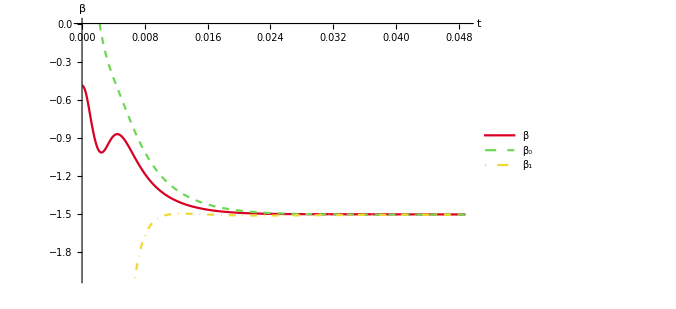

./Desktop/projects/QC_Burgers/code_revise2/beta260311.pdf

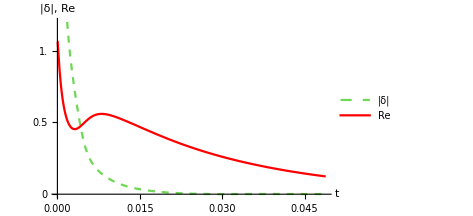

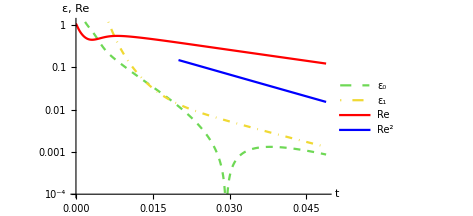

./Desktop/projects/QC_Burgers/code_revise2/Re260311.pdf

```mathematica
beta={};
beta0={};
beta1={};
ratiobeta0={};
ratiobeta1={};
test={};
For[t=1,t<=3500,t++,betaa=Sum[uresults[[t]][[i]]^4,{i,1,xgr}]*xgr/Sum[uresults[[t]][[i]]^2,{i,1,xgr}]^2-3;
betab=Sum[approxuresults[[t]][[i]]^4,{i,1,xgr}]*xgr/Sum[approxuresults[[t]][[i]]^2,{i,1,xgr}]^2-3;
betac=Sum[approxuresults[[t]][[i]]^4*(5.-4.*results[[t]][[i]]/hom),{i,1,xgr}]*xgr/Sum[approxuresults[[t]][[i]]^2*(3.-2.*results[[t]][[i]]/hom),{i,1,xgr}]^2-3.;
AppendTo[beta,{tMin+t*dt,betaa}];
AppendTo[beta0,{tMin+t*dt,betab}];
AppendTo[beta1,{tMin+t*dt,betac}];
AppendTo[ratiobeta0,{tMin+t*dt,Abs[1-betab/betaa]}];
AppendTo[ratiobeta1,{tMin+t*dt,Abs[1-betac/betaa]}];
AppendTo[test,{tMin+t*dt,Exp[-40*(tMin+t*dt)]}]];

graph11=ListLinePlot[{beta[[1;;2000]],beta0[[1;;2000]],beta1[[1;;2000]]}, PlotRange->{-2,0},BaseStyle->{FontSize->17},PlotStyle->{brown,{Dashed,green},{DotDashed,beige}},ImageSize->500,PlotRangeClipping->False,PlotLegends->Placed[LineLegend[{"β",Subscript["β",0],Subscript["β",1]}],{Right,Center}],AxesLabel->{"t","β"}]
Export["beta.pdf",%]
graph12=ListLinePlot[{ratiobeta0[[1;;2000]],Reynolds[[1;;2000]]},PlotRange->{0,1.2},BaseStyle->{FontSize->12},ImageSize->350,PlotStyle->{{Dashed,green},Red},PlotRangeClipping->False,PlotLegends->Placed[LineLegend[{"|δ|","Re"}],{Right,Center}],Ticks->{Automatic,{0,0.5,1.0,1.5}},AxesLabel->{"t","|δ|, Re"}]
graph13=ListLogPlot[{ratiobeta0[[1;;2000]],ratiobeta1[[1;;2000]],Reynolds[[1;;2000]],Reynolds2[[820;;2000]]},PlotRange->{0.0001,1.2},BaseStyle->{FontSize->12},ImageSize->350,PlotStyle->{{Dashed,green},{DotDashed,beige},Red,Blue},PlotRangeClipping->False,PlotLegends->Placed[LineLegend[{Subscript["ε",0],Subscript["ε",1],"Re",Superscript["Re",2]}],{Left,Bottom}],Joined->True,Ticks->{Automatic,{0.001,0.01,0.1,1.0}},AxesLabel->{"t","ε, Re"}]
Export["Re.pdf",%]

(*test*)
graph1313=ListLogPlot[test[[1;;3500]]];
```